## (*Matrices and vectors needed*) Here we consider a 3-state model (0, 1 or 2 motors) of cargo transport in one direction (N=2)

```mathematica
(*Transition probability matrix*)
```

```mathematica
P = {{0,1,0},{eps1/(eps1+pi1),0,pi1/(eps1+pi1)},{0,1,0}}//MatrixForm
```

(0 | 1 | 0
eps1/(eps1+pi1) | 0 | pi1/(eps1+pi1)
0 | 1 | 0)

```mathematica
(*Set first state as absorbing*)
```

```mathematica
Pabs = {{1,0,0},{eps1/(eps1+pi1),0,pi1/(eps1+pi1)},{0,1,0}}
```

{{1,0,0},{eps1/(eps1+pi1),0,pi1/(eps1+pi1)},{0,1,0}}

```mathematica
Pabs//MatrixForm
```

(1 | 0 | 0
eps1/(eps1+pi1) | 0 | pi1/(eps1+pi1)
0 | 1 | 0)

```mathematica
(*Extract 2 by 2 matrix in the lower bottom corner from Pabs: Ptilde in text*)
```

```mathematica
q ={{0,pi1/(eps1+pi1)},{1,0}}
```

{{0,pi1/(eps1+pi1)},{1,0}}

```mathematica
q//MatrixForm
```

(0 | pi1/(eps1+pi1)
1 | 0)

```mathematica
(*Elements of the first row of P corresponding to the transient states*)
```

```mathematica
Pinit = {1,0}
```

{1,0}

```mathematica
(*First moments of rewards and times in each transient state*)
```

```mathematica
rvect = {v1/(eps1+pi1),v2/(eps2)}
```

{v1/(eps1+pi1),v2/eps2}

```mathematica
tvect = {1/(eps1+pi1),1/(eps2)}
```

{1/(eps1+pi1),1/eps2}

```mathematica
(*Cross-moment of reward and time in each transient state*)
```

```mathematica
rtvect={2*v1/(eps1+pi1)^2,2*v2/(eps2)^2}
```

{(2 v1)/(eps1+pi1)^2,(2 v2)/eps2^2}

```mathematica
(*Second moments of rewards and times in each transient state*)
```

```mathematica
r2vect = {2*v1^2/(eps1+pi1)^2,2*v2^2/(eps2)^2}
```

{(2 v1^2)/(eps1+pi1)^2,(2 v2^2)/eps2^2}

```mathematica
t2vect = {2/(eps1+pi1)^2,2/(eps2)^2}
```

{2/(eps1+pi1)^2,2/eps2^2}

```mathematica
(*Calculate moments given start in a state*)
```

```mathematica
(*Identity matrix*)
```

```mathematica
imat={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
imat//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
(*Check that determinant of I-Q is positive*)
```

```mathematica
Det[imat-q]
```

eps1/(eps1+pi1)

```mathematica
(*Calculate inverse of I-Q*)
```

```mathematica
mmat = FullSimplify[Inverse[imat-q]]
```

{{(eps1+pi1)/eps1,pi1/eps1},{(eps1+pi1)/eps1,(eps1+pi1)/eps1}}

```mathematica
mmat//MatrixForm
```

((eps1+pi1)/eps1 | pi1/eps1
(eps1+pi1)/eps1 | (eps1+pi1)/eps1)

```mathematica
(*Set up diagonal matrices with moments of rewards and times*)
```

```mathematica
diagr =DiagonalMatrix[rvect]
```

{{v1/(eps1+pi1),0},{0,v2/eps2}}

```mathematica
diagt = DiagonalMatrix[tvect]
```

{{1/(eps1+pi1),0},{0,1/eps2}}

```mathematica
(*Moments of rewards and times given start in each state*)
```

```mathematica
uvectr = FullSimplify[mmat.rvect]
```

{(eps2 v1+pi1 v2)/(eps1 eps2),(eps2 v1+(eps1+pi1) v2)/(eps1 eps2)}

```mathematica
uvectt = FullSimplify[mmat.tvect]
```

{(eps2+pi1)/(eps1 eps2),(eps1+eps2+pi1)/(eps1 eps2)}

```mathematica
uvectrt =mmat.(rtvect+diagr.q.uvectt+diagt.q.uvectr) ;(*FullSimplify[mmat.rtvect]*)
```

```mathematica
vvectr = mmat.(r2vect+2.diagr.q.uvectr);
```

```mathematica
vvectt = mmat.(t2vect+2.diagt.q.uvectt);
```

```mathematica
(*Final Calculations*)
```

```mathematica
ex = FullSimplify[0+uvectr.Pinit]
```

(eps2 v1+pi1 v2)/(eps1 eps2)

```mathematica
et = FullSimplify[(1/pi0)+uvectt.Pinit]
```

1/pi0+(eps2+pi1)/(eps1 eps2)

```mathematica
(*Effective velocity (classical theory)*)
```

```mathematica
Vinf = FullSimplify[ex/et]
```

(pi0 (eps2 v1+pi1 v2))/(eps1 eps2+pi0 (eps2+pi1))

```mathematica
ext=0+0+(1/pi0)*(uvectr.Pinit)+ uvectrt.Pinit;
```

```mathematica
ex2=0+2*0*(uvectr.Pinit)+vvectr.Pinit;
```

```mathematica
et2=(2/pi0^2)+2*(1/pi0)*(uvectt.Pinit)+vvectt.Pinit;
```

```mathematica
varx=ex2-ex^2;
```

```mathematica
vart=et2-et^2;
```

```mathematica
vartx = ext-et*ex;
```

```mathematica
(*Effective diffusivity (classical theory)*)
```

```mathematica
Dinf = FullSimplify[(Vinf^2*vart+varx-2*Vinf*vartx)/(2*et)]
```

(eps2 pi0 (eps1^3 pi1 v2^2+pi0^2 pi1^2 (v1^2-2. v1 v2+1. v2^2)+eps1^2 (eps2^2 v1^2+2. eps2 pi1 v1 v2+pi1 v2 (-2. pi0 v1+2. pi0 v2+2. pi1 v2))+eps1 pi1 (1. eps2^2 v1^2+2. eps2 pi1 v1 v2+1. pi1^2 v2^2+pi0 pi1 v2 (-2. v1+2. v2)+pi0^2 (v1^2-2. v1 v2+v2^2))))/((eps1+pi1) (eps1 eps2+pi0 (eps2+pi1))^3)

```mathematica
(*Parameters and dependencies*)
Set up model parameters for a range of load forces and linear motors
```

```mathematica
v = 1
```

1

```mathematica
epsil = 1
```

1

```mathematica
Fs = 6
```

6

```mathematica
Fd = 3
```

3

```mathematica
piad = 5
```

5

```mathematica
w = 1
```

1

```mathematica
F1 = {0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6}
```

{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6}

```mathematica
F2 = {6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}
```

{6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

```mathematica
F=Join[F1,F2]
```

{0,0.5,1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9,9.5,10,10.5,11,11.5,12}

```mathematica
eps1 = epsil*Exp[F/Fd]
```

{1,1.18136,ⅇ^(1/3),1.64872,ⅇ^(2/3),2.30098,ⅇ,3.21127,ⅇ^(4/3),4.48169,ⅇ^(5/3),6.2547,ⅇ^2,8.72914,ⅇ^(7/3),12.1825,ⅇ^(8/3),17.002,ⅇ^3,23.7283,ⅇ^(10/3),33.1155,ⅇ^(11/3),46.2163,ⅇ^4}

```mathematica
eps2 = 2*epsil*Exp[F/(2*Fd)]
```

{2,2.17381,2 ⅇ^(1/6),2.56805,2 ⅇ^(1/3),3.03379,2 √ⅇ,3.584,2 ⅇ^(2/3),4.234,2 ⅇ^(5/6),5.00188,2 ⅇ,5.90902,2 ⅇ^(7/6),6.98069,2 ⅇ^(4/3),8.24671,2 ⅇ^(3/2),9.74233,2 ⅇ^(5/3),11.5092,2 ⅇ^(11/6),13.5965,2 ⅇ^2}

```mathematica
v1=Join[v*(1-(F1/Fs)^w),ConstantArray[0,12]]
```

{1,0.916667,5/6,0.75,2/3,0.583333,1/2,0.416667,1/3,0.25,1/6,0.0833333,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v2 = v*(1-(F/(2*Fs))^w)
```

{1,0.958333,11/12,0.875,5/6,0.791667,3/4,0.708333,2/3,0.625,7/12,0.541667,1/2,0.458333,5/12,0.375,1/3,0.291667,1/4,0.208333,1/6,0.125,1/12,0.0416667,0}

```mathematica
pi0 = 2*piad
```

10

```mathematica
pi1=piad
```

5

```mathematica
N[Dinf]
```

{0.00289352,0.00351649,0.00426837,0.00511791,0.00601968,0.00691453,0.00773228,0.00839737,0.00883744,0.00899455,0.00883709,0.00836957,0.00763687,0.00590205,0.00440348,0.00315744,0.00216423,0.00140852,0.000862254,0.00048945,0.000251479,0.000111698,0.0000386184,7.41176×10^-6,0.}

```mathematica
N[Vinf]
```

{0.972222,0.913023,0.851777,0.788472,0.723164,0.655994,0.587215,0.51721,0.446515,0.375824,0.305991,0.238009,0.172966,0.142631,0.115448,0.0915308,0.070901,0.0534819,0.0391031,0.0275142,0.0184074,0.0114422,0.00627059,0.00255829,0.}

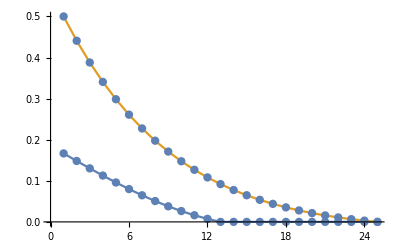

```mathematica
ListLinePlot[%67,Mesh->All]
```